```mathematica
Clear["Global`*"];

SphVec[θ_,ϕ_]:={Cos[θ],Cos[ϕ]*Sin[θ],Sin[θ]*Sin[ϕ]};

(*SG Function*)
G[v_,{p_,λ_,μ_}]:=μ*Exp[λ*(Dot[v,p]-1)];
Print[">SG:"  TraditionalForm[G[v,{p,λ,μ}]]];
```

>SG: (μ ⅇ^(λ (v.p-1)))

```mathematica
(*θ must between -π/2 and π/2*)
GSimple[θ_,λ_,μ_]:=μ*Exp[λ*(Cos[θ]-1)];
SGCircle[θ_,λ_,μ_]:=Module[{y},
y=GSimple[θ,λ,μ];
{N[θ],N[y]}
];

Print[">Plot 2D SG:"]
Manipulate[ParametricPlot[SGCircle[θ,λ,μ],
{θ,-π/2,π/2}, PlotRange->{{-3,3},{-3,3}},AspectRatio->1],
{λ,2.133,20},{μ,1,10}]
```

>Plot 2D SG:

```mathematica
DotClamp[a_,b_]:=Max[0,Dot[a,b]];
sgEvaluate[v_,sg_]:=G[v,sg];
sgIntegral[λ_,μ_:1]:=μ*2π*(1-Exp[-2λ])/λ;
Print[">SG Integral:" TraditionalForm[sgIntegral[λ,μ]]];
```

>SG Integral: (2 π (1-ⅇ^(-2 λ)) μ)/λ

```mathematica
(*https://www.astronomyclub.xyz/celestial-sphere-2/solid-angle-on-the-celestial-sphere.html*)
solidAngleIntegral[func_]:=Integrate[func*Sin[θ],{θ,0,π},{ϕ,0,2π}];
sgIntegral1=solidAngleIntegral[μ*Exp[λ(Cos[θ]-1)]];
Print[">Analytic SG Integral:" TraditionalForm[sgIntegral1]];
```

>Analytic SG Integral: (2 π (1-ⅇ^(-2 λ)) μ)/λ

```mathematica
epsilonIntegral[func_]:=Integrate[func*Sin[θ],{θ+ϕ,0,π}];
sgIntegralEps=epsilonIntegral[μ*Exp[λ(Cos[θ]-1)]];
TraditionalForm[sgIntegralEps]
```

Integrate::ilim: Invalid integration variable or limit(s) in {θ+ϕ,0,π}.

∫_0^π μ sin(θ) ⅇ^(λ (cos(θ)-1))ⅆ(θ+ϕ)

```mathematica
p0={0,0,1};
λ0=2.133;
μ0=1.170;
sg0={p0,λ0,μ0};
G1[θ_,ϕ_,{p_,λ_,μ_}]:=Module[{v},v=SphVec[θ,ϕ]; Sin[θ]*G[v, {p,λ,μ}]];
N1=SetPrecision[NIntegrate[G1[θ,ϕ,sg0],{θ,0,π},{ϕ,0,2π}],5];
N2=SetPrecision[sgIntegral[λ0,μ0],5];
Print[">Validate Numerics(Solid Angle) Integral:" (N1==N2)];
```

>Validate Numerics(Solid Angle) Integral: True

```mathematica
sgDot[{p1_,λ1_,μ1_},{p2_,λ2_,μ2_}]:=4π*μ1*μ2*Sinh[Norm[p1*λ1+p2*λ2]]/(Exp[λ1+λ2]*Norm[p1*λ1+p2*λ2]);
Print[">SG Dot:" TraditionalForm[sgDot[{p1,λ1,μ1},{p2,λ2,μ2}]]];
```

>SG Dot: (4 π μ1 μ2 ⅇ^(-λ1-λ2) sinh(Norm[p1 λ1+p2 λ2]))/Norm[p1 λ1+p2 λ2]

```mathematica
Energy0=sgIntegral[λ0,μ0];
Print[">Energy Conservation, Solve μ:" Solve[Energy0==sgIntegral[λ,μ],μ]];
```

{{>Energy Conservation, Solve μ: (μ→(0.540823 λ)/(1.-1. ⅇ^(-2. λ)))}}

```mathematica
sgFindMu[λ_,targetIntegral_]:=targetIntegral/(sgIntegral[λ,1]);
Print[">Analytic Solve μ:"];
sgFindMu[Subscript[λ,x],sgIntegral[λ,μ]]
```

>Analytic Solve μ:

((1-ⅇ^(-2 λ)) μ λ_x)/((1-ⅇ^(-2 λ_x)) λ)

>Plot μ with energy π:

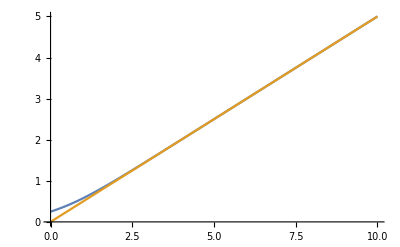

```mathematica
Print[">Plot μ with energy π:"]
Plot[{sgFindMu[λ,π],λ/2},{λ,0,10}]
```

```mathematica
NSolve[sgIntegral[x]==π,x,Reals];
sgIntegral[1.9603451974364432];
(*https://seblagarde.wordpress.com/2012/06/03/spherical-gaussien-approximation-for-blinn-phong-phong-and-fresnel/#more-822*)
Print[">vMF Integral Equation: " ];
4π*Exp[-x]*Sinh[x]/x
Plot[{(4π*Exp[-x]*Sinh[x]/x)-sgIntegral[x]},{x,0,10}]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

>vMF Integral Equation:

(4 ⅇ^-x π Sinh[x])/x

-Graphics-

```mathematica
Print[">Spherical Integrals"];
Integrate[Sin[θ]*Max[0,Cos[θ]],{θ,0,π},{ϕ,0,2π}]
Integrate[1,{x,y,z}∈Sphere[]]
Integrate[DotClamp[v,{0,0,1}],v∈Sphere[]]
```

>Spherical Integrals

π

4 π

π

Fit SG Integral

>Original Integral:

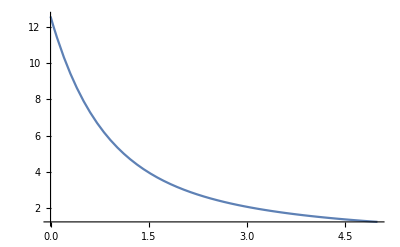

```mathematica
Print[">Original Integral:"];
Plot[sgIntegral[λ],{λ,0,5},PlotRange->Full]
```

```mathematica
FindMinimum[NIntegrate[Abs[sgIntegral[λ]-(a+b/λ)],{λ,2,50}],{a,1.0},{b,2.0}]
```

NIntegrate::inumr: The integrand Abs[-a-b/λ+(2 (1-ⅇ^(-2 λ)) π)/λ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2,50}}.

NIntegrate::inumr: The integrand Abs[-1. (a+b/λ)+(2 (1-ⅇ^(-2 λ)) π)/λ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2.,50.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0237404,{a→1.52722×10^-6,b→6.28314}}

>Fit Errors:

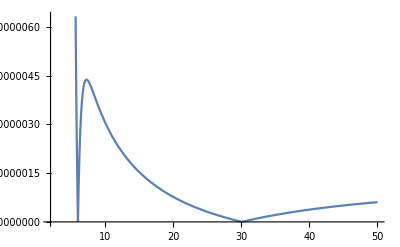

```mathematica
Print[">Fit Errors:"];
Plot[Abs[sgIntegral[λ]-( 1.527220889220148*^-6+6.283139334605482/λ)],{λ,2,50}]
```